```mathematica
Needs["QNMspectral`"]
```

```mathematica
F[u_,Q_]:=1-(2(4+Q^2)/8)*u^3+(Q^2/4)*u^4;
```

```mathematica
ncrd=4;
coord={t,u,x,y};
metric={{F[u,Q]/u^2,1/u^2,0,0},{1/u^2,0,0,0},{0,0,1/u^2,0},{0,0,0,1/u^2}};
inversemetric=Simplify[Inverse[metric]];
```

```mathematica
metric//MatrixForm
```

((1-1/4 (4+Q^2) u^3+(Q^2 u^4)/4)/u^2 | 1/u^2 | 0 | 0
1/u^2 | 0 | 0 | 0
0 | 0 | 1/u^2 | 0
0 | 0 | 0 | 1/u^2)

```mathematica
Am[1]=-Q*u;
Am[2]=0;
Am[3]=0;
Am[4]=0;
```

```mathematica
P1[t,u,x,y]=R[u]*E^(-I*ω*t);
```

```mathematica
g=Simplify[Det[metric]]
```

-1/u^8

```mathematica
scalareq=Sum[-(1/Sqrt[-g])D[Sqrt[-g]*inversemetric[[i,j]]*(D[P1[t,u,x,y],coord[[j]]]-I*Am[j]*P1[t,u,x,y]),coord[[i]]]+I*Am[i]*inversemetric[[i,j]]*(D[P1[t,u,x,y],coord[[j]]]-I*Am[j]*P1[t,u,x,y]),{i,1,4},{j,1,4}]+2P1[t,u,x,y];
```

```mathematica
eqR=Simplify[scalareq]
```

1/4 ⅇ^(-ⅈ t ω) ((8+4 ⅈ Q u^2-8 ⅈ u ω) R[u]+u ((-8 ⅈ Q u^2+Q^2 u^3 (-1+2 u)-4 (2+u^3-2 ⅈ u ω)) R'[u]+u (4-(4+Q^2) u^3+Q^2 u^4) R''[u]))

```mathematica
eqR0=(Exp[ⅈ (ω t)]/u^3)PowerExpand[eqR]//Collect[#,_[u],Simplify]&
```

((2+ⅈ Q u^2-2 ⅈ u ω) R[u])/u^3+(-2 ⅈ Q+1/4 Q^2 u (-1+2 u)-(2+u^3-2 ⅈ u ω)/u^2) R'[u]+((4-(4+Q^2) u^3+Q^2 u^4) R''[u])/(4 u)

```mathematica
Series[u^-p eqR0/.R->(#^p&),{u,0,-3}]//Normal
Solve[%==0,p]
```

(2-3 p+p^2)/u^3

{{p→1},{p→2}}

```mathematica
eqR2=u^2 eqR0/.R->(#^1 δRfin[#]&)//Collect[#,f_[u],Simplify]&
```

1/4 u^2 (-4 ⅈ Q-4 u+Q^2 u (-1+2 u)) δRfin[u]+(-2 ⅈ Q u^3-3 u^4+Q^2 (-(3 u^4)/4+u^5)+2 ⅈ u^2 ω) δRfin'[u]+1/4 u^2 (4-(4+Q^2) u^3+Q^2 u^4) δRfin''[u]

```mathematica
Series[eqR2,{u,0,0}]
Series[u^-p eqR2/.δRfin->(#^p&)//Expand,{u,0,0}]//Normal
Solve[%==0,p]
```

O[u]^2

-p+p^2

{{p→0},{p→1}}

```mathematica
modes=GetModes[eqR2/.Q->2.5,{100,0}];//AbsoluteTiming
```

{0.115779,Null}

```mathematica
(*Para el caso de Q=0 SCHWARZHILD ADS*)
```

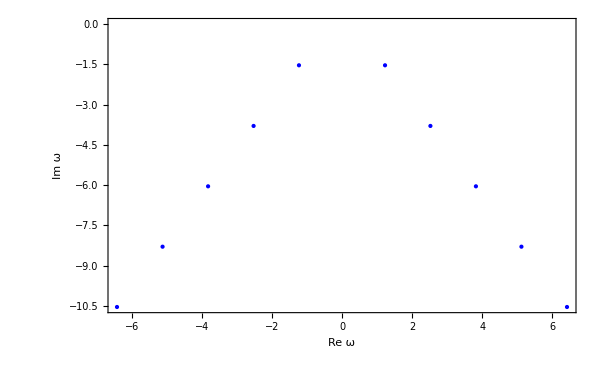
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.22788991566654 | -1.533301335713256
2 | ± 2.522743403619 | -3.793686173993
3 | ± 3.821279112 | -6.0441867597
4 | ± 5.1201 | -8.29425
5 | ± 6.4 | -10.5}

```mathematica
modesAccurate1= GetAccurateModes[eqR2/.Q->0,{40},{100}];

ShowModes[modesAccurate1,Precision ->Infinity]
```

```mathematica
Export["SchwarAdS4s.png",ShowModes[modesAccurate1,Precision ->Infinity]]
```

SchwarAdS4s.png

```mathematica
SystemOpen["SchwarAdS4s.png"]
```

```mathematica
SystemOpen["SchwarAdS4.png"]
```

```mathematica
(*Para el caso Q=2.5, RN ADS*)
```

```mathematica
modesAccurate2= GetAccurateModes[eqR2/.Q->2.5,{40},{100}];
```

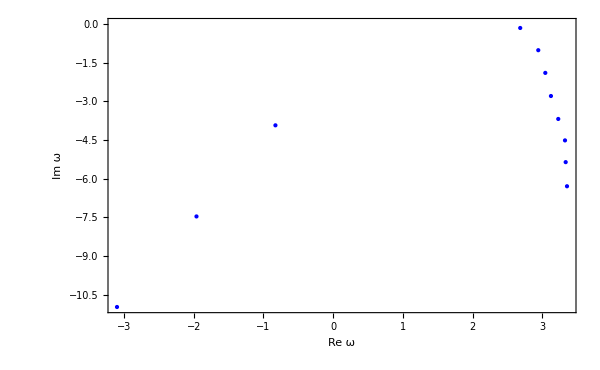
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 2.68371290574512 | -0.1483027802639
2 | ± 2.9428065073219416 | -1.011035370869434
3 | ± 3.0436856266335 | -1.891666960944
4 | ± 3.12462289 | -2.78945032
5 | ± 3.229512 | -3.6802053
6 | ± 0.828402205446 | -3.927128580459
7 | ± 3.3262 | -4.51228
8 | ± 3.34 | -5.356
9 | ± 3. | -6.3
10 | ± 1.96115 | -7.464165
11 | ± 3.1 | -11.}

```mathematica
ShowModes[modesAccurate2,Precision ->Infinity]
```

```mathematica
Export["RNAdS4i.png",ShowModes[modesAccurate2,Precision ->Infinity]]
```

RNAdS4i.png

```mathematica
SystemOpen["RNAdS4i.png"]
```